# Linear model of the mechanical HOTI

```mathematica
SetDirectory[NotebookDirectory[]];
<<"chiralGraph.m"
<<"chiralMechanics.m"
```

## Definition of the linear system based on the experimental model

```mathematica
(*Model dependent part*)
ax=ay=60.;
r=18. √2;
Clear[keysBeadsUC,pairKeysUC,posBeadsUC,identityUC,translationOp,posPivotsUC];
{keysBeadsUC[i_,j_],pairKeysUC[i_,j_],identityUC,posBeadsUC,translationOp[i_,j_],posPivotsUC}=Module[{keysBeads,posBeads,pairKeys,identity,l={i,j},pVec1,pVec2,transOp,posPivots},
Clear[a,b,c];
(*definition of beads and connectivity*)
keysBeads=#@@l&/@{a,b,c,d};
pairKeys={{a@@l,b@@l},{b@@l,c@@l},{c@@l,d@@l},{c@@l,b@@(l+{1,0})},{d@@l,a@@(l+{1,0})},{a@@l,b@@(l+{0,1})}};

(*primitive vectors and positions*)
pVec1=2{ax,0};
pVec2=2{0,ay};
transOp={pVec1} i +{pVec2} j;
posPivots={{0,0},{0,-ay},{ax,-ay},{ax,0}};
posBeads=MapThread[posPivots[[#1]]+r AngleVector[#2]&,{Range[4],{-π/4,-3π/4,3π/4,π/4}}];
identity={1,1,1,0};

{keysBeads,pairKeys,identity,posBeads,transOp,posPivots}
];

{keysBeads,pairKeysBeads,identity,posBeads,posPivots}=tesselate[{4,3},keysBeadsUC,pairKeysUC,identityUC,posBeadsUC,translationOp,posPivotsUC];
```

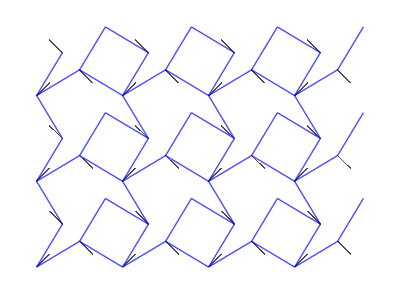

```mathematica
beadAndSpringGraphic2D[{keysBeads,pairKeysBeads,identity,posBeads,posPivots}]
```

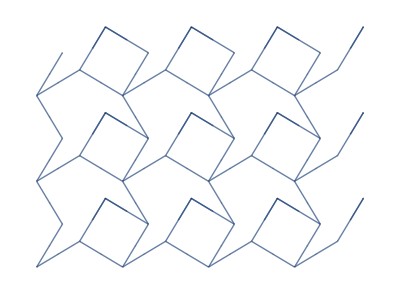

```mathematica
graphBeads=eqSystem[keysBeads,pairKeysBeads,AssociationThread[keysBeads,posBeads]];
graphPert=pertSystem[graphBeads,AssociationThread[keysBeads,identity],AssociationThread[keysBeads,posBeads],AssociationThread[keysBeads,posPivots]]
```

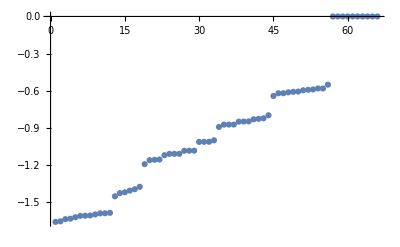

```mathematica
{{negEval,negEvec},{zmEval,zmEvec}}=negativeAndZMspectrum[Normal[WeightedAdjacencyMatrix[graphPert]],0.01];
{projA,projB}={projAList[#],projBList[#]}&@graphPert;
ListPlot[negEval~Join~zmEval]
```

```mathematica
{localBasis,accuracyList}=localizedBasisPencilMatrix[graphPert,negEvec,0.2];
```

#### Zero-energy modes

```mathematica
c=chiralList[graphPert];
positions=positionList[graphPert];
pA=(ConstantArray[1,Length@c]+c)/2;
pB=(ConstantArray[1,Length@c]-c)/2;
```

```mathematica
Max@Total[Abs@zmEvec]
```

2.16674

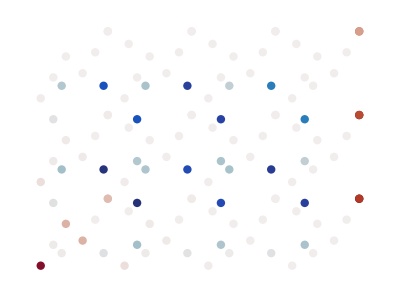

```mathematica
max=Max@Total[Abs@zmEvec];
listBlue=ToExpression@;
listRed=ToExpression@;
balanceRedColorMap=Blend[Reverse[RGBColor[#]&/@listRed],#]&;
balanceBlueColorMap=Blend[Reverse[RGBColor[#]&/@listBlue],#]&;
zmPlot=Graphics[{MapThread[{balanceRedColorMap[Abs@#2/max],Disk[#1,ax/10]}&,{positions,pA Total[Abs@zmEvec]}][[Flatten[Position[pA,1]]]],MapThread[{balanceBlueColorMap[Abs@#2/max],Disk[#1,ax/10]}&,{positions,pB Total[Abs@zmEvec]}][[Flatten[Position[pB,1]]]]}]
```

#### Chiral polarization field

```mathematica
positions=positionList[graphPert];
chiral=chiralList[graphPert];
```

```mathematica
momentsList=Quiet@Map[With[{norm2=(#*.#)},
{
Sqrt[norm2],
(#*.(chiral#))/norm2,
1/norm2(#*.(positions[[All,1]]#)),
1/norm2(#*.(positions[[All,2]]#)),
1/norm2(#*.(chiral positions[[All,1]]#)),
1/norm2(#*.(chiral positions[[All,2]]#))
}]&,localBasis];
```

```mathematica
fieldData=Map[{#[[3]],#[[4]],2(#[[5]]-#[[2]]#[[3]]),2(#[[6]]-#[[2]]#[[4]])}&,momentsList];
```

```mathematica
fcolor=GrayLevel[(120-#)/120]&;
barl=BarLegend[{fcolor[#]&,{0,40}},LegendLabel->"Norm",LabelStyle->Directive[Black,FontSize->14]];
primitivesList=Map[Module[{center={#1[[1]],#1[[2]]},pol={#1[[3]],#1[[4]]},unitvector,norm,circleRadius=15},
norm=Norm@pol;
unitvector=Normalize[pol];
{fcolor[norm],Thickness[0.005],Arrowheads[.02],Arrow[{center-unitvector circleRadius,center+unitvector circleRadius}],Thickness[0.002],Circle[center,circleRadius]}
]&,fieldData];
```

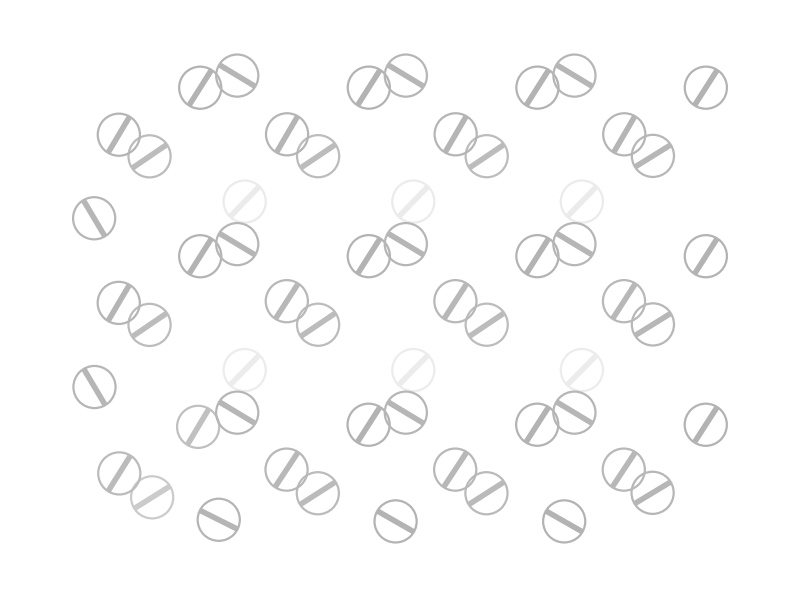

```mathematica
Graphics[primitivesList]
```

#### Centers

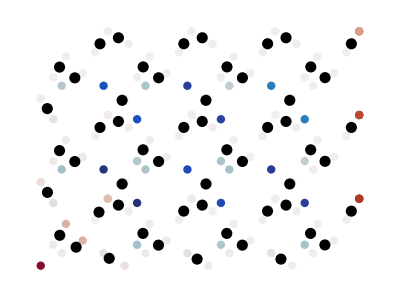

```mathematica
centers=momentsList[[All,{3,4}]];
refImage=Show[zmPlot,ListPlot[centers,AspectRatio->Automatic,Frame->True,FrameTicks->None,PlotStyle->{{PointSize[0.02],Black}}]]
```

#### Definition of chiral molecules

```mathematica
regionList={};
DynamicModule[{delimiters={}},
Row@{ClickPane[Show[{refImage,Graphics[{Red,Line[Dynamic[delimiters]]}],Graphics[{Blue,Dynamic@regionList}]},ImageSize->Large],AppendTo[delimiters,#1]&],Button["addMolecule",{AppendTo[regionList,Polygon[delimiters]],delimiters={}}]}
]
```

```mathematica
(*Export["moleculesMechanicalHOTI-PureWannier.mx",regionList]*)
```

```mathematica
regionList=Import["moleculesMechanicalHOTI-PureWannier.mx"];
```

#### Coarse-grained field

```mathematica
rmemberfList=RegionMember[#]&/@regionList;
whichCell[{x_,y_}]:=Module[{i,isMember},
i=1;
isMember=rmemberfList[[i]][{x,y}];
While[isMember==False,isMember=rmemberfList[[i]][{x,y}];i++];
i
]
```

```mathematica
meanDataList=fieldDataᵀ;
```

```mathematica
groupByDistanceTimeAverageData=Gather[meanDataListᵀ,whichCell[{#1[[1]],#1[[2]]}]==whichCell[{#2[[1]],#2[[2]]}]&];
coarseGrainedField=({Mean[#[[1]]],Mean[#[[2]]],Total[#[[3]]],Total[#[[4]]]}&@(#ᵀ))&/@groupByDistanceTimeAverageData;
```

```mathematica
groupByDistanceTimeSTDPolData=Gather[(meanDataList[[{1,2}]]~Join~(stdDataList[[{3,4}]]))ᵀ,whichCell[{#1[[1]],#1[[2]]}]==whichCell[{#2[[1]],#2[[2]]}]&];
coarseGrainedSTDPolData=(Sqrt[(#.#)/Length[#]^2]&/@(#[[All,{3,4}]]ᵀ))&/@groupByDistanceTimeSTDPolData;
```

```mathematica
coarseGrainedMeanAngles=ArcTan@@#&/@(coarseGrainedField[[All,{3,4}]]);
```

```mathematica
dfdx[x_,y_]=D[ArcTan[x,y], x];
dfdy[x_,y_]=D[ArcTan[x,y], y];
coarseGrainedSTDAngleData=MapThread[Sqrt[((dfdx@@#1)#2[[1]])^2+((dfdy@@#1)#2[[2]])^2]&,{coarseGrainedField[[All,{3,4}]],coarseGrainedSTDPolData}];
```

#### Graphics

```mathematica
fcolor=GrayLevel[(120-#)/120]&;
barl=BarLegend[{fcolor[#]&,{0,40}},LegendLabel->"Norm",LabelStyle->Directive[Black,FontSize->14]];
primitivesList=MapThread[Module[{center={#1[[1]],#1[[2]]},pol={#1[[3]],#1[[4]]},unitvector,norm,circleRadius=30},
norm=Norm@pol;
unitvector=Normalize[pol];
{fcolor[norm],Thickness[0.01],Arrow[{center-unitvector circleRadius,center+unitvector circleRadius}],Thickness[0.005],Circle[center,circleRadius],Thickness[0.02],Circle[center,circleRadius,{#2-#3,#2+#3}]}
]&,{coarseGrainedField,coarseGrainedMeanAngles,coarseGrainedSTDAngleData}];
```

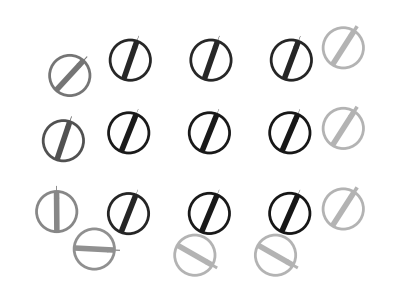

```mathematica
Graphics[primitivesList]
```

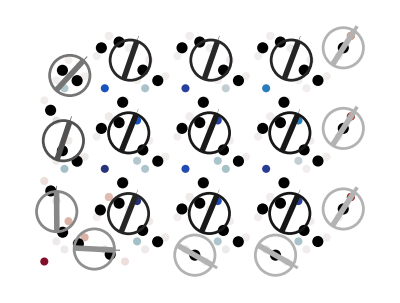

```mathematica
Show[refImage,Graphics[primitivesList]]
```

#### Singularity of the chiral polarization

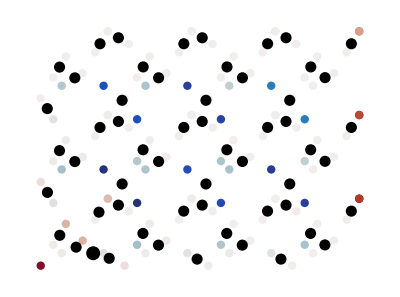

```mathematica
Show[refImage,Graphics[Disk[coarseGrainedField[[1,;;2]],10]]]
```

```mathematica
(coarseGrainedField2[[1,3;;]].{1,0}+coarseGrainedField2[[2,3;;]].{0,1})
```

```mathematica
207.8536047589261
```

207.854

## Validation: evolution of local responses

```mathematica
h=Normal[WeightedAdjacencyMatrix[graphPert]];
chiral=chiralList[graphPert];
positions=positionList[graphPert];
pA=(ConstantArray[1,Length@c]+c)/2;
pB=(ConstantArray[1,Length@c]-c)/2;
```

### Wannier initial condition

```mathematica
{{negEval,negEvec},{zmEval,zmEvec}}=negativeAndZMspectrum[Normal[WeightedAdjacencyMatrix[graphPert]],0.01];
{icWannierList,accuracyList}=localizedBasisPencilMatrix[graphPert,negEvec,0.2];
```

#### Evolution

```mathematica
tf=40;
dt=0.1;
solList=NDSolve[{ⅈ x'[t]==-(h).x[t],x[0]==#},x,{t,0,tf}]&/@icWannierList;
solTable=Table[(x[#]/.sol[[1]])&/@Range[0,tf,dt],{sol,solList}];
```

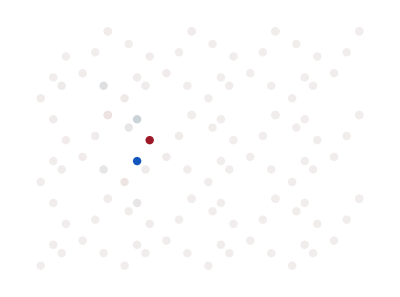

```mathematica
balanceRedColorMap=Blend[Reverse[RGBColor[#]&/@listRed],#]&;
balanceBlueColorMap=Blend[Reverse[RGBColor[#]&/@listBlue],#]&;
Graphics[{MapThread[{balanceRedColorMap[Abs@#2],Disk[#1,ax/10]}&,{positions,pA solTable[[25,1]]}][[Flatten[Position[pA,1]]]],MapThread[{balanceBlueColorMap[Abs@#2],Disk[#1,ax/10]}&,{positions,pB solTable[[25,1]]}][[Flatten[Position[pB,1]]]]}]
```

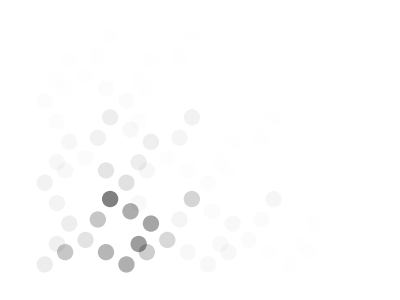

```mathematica
Graphics[MapThread[{Opacity[Abs[#2]],Disk[#1,ax/5]}&,{positions,solTable[[1,100]]}]]
```

#### Moments

```mathematica
momentsList=Quiet@Map[With[{norm2=(#*.#)},
{
Sqrt[norm2],
(#*.(chiral#))/norm2,
1/norm2(#*.(positions[[All,1]]#)),
1/norm2(#*.(positions[[All,2]]#)),
1/norm2(#*.(chiral positions[[All,1]]#)),
1/norm2(#*.(chiral positions[[All,2]]#))
}]&,#]&/@solTable;
```

```mathematica
(*Color map functions*)
githubTextToList[text_String]:=ToExpression[StringReplace[text,{"["->"{","]"->"}"}]];
listViridis=;
viridisCM=Blend[RGBColor[#]&/@listViridis,#]&;
colorNodes=With[{n=Length[icWannierList]},viridisCM[(#-1)/(n-1)]&/@Range[n]];
optionsListPlot={Joined->True,Frame->True,ImageSize->500,PlotRange->All,BaseStyle->{FontSize->25},LabelStyle->Black,FrameStyle->Directive[Black]};
```

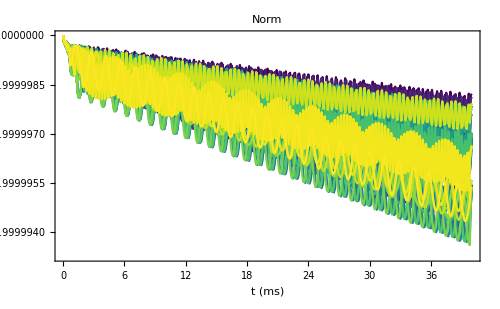
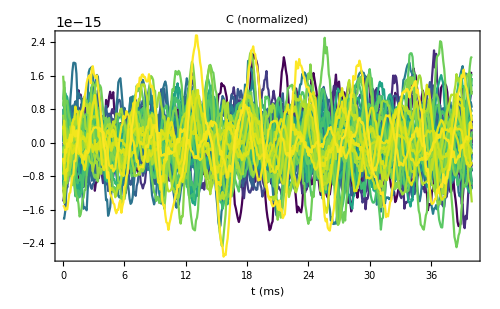
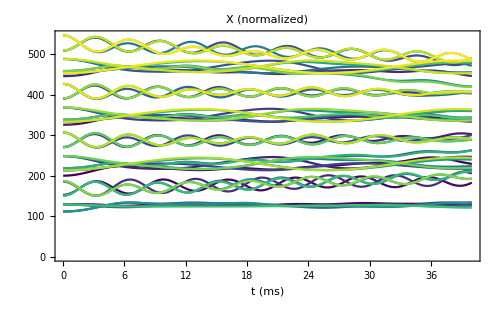
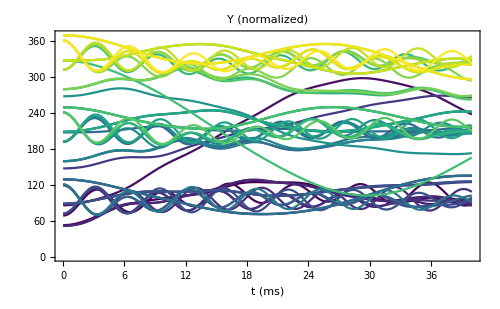
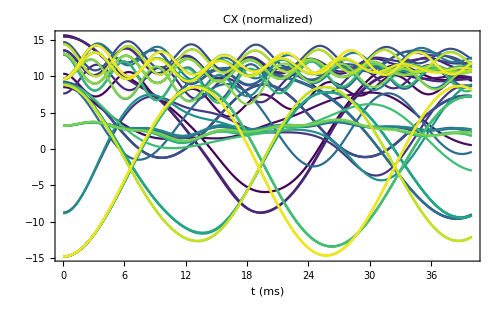
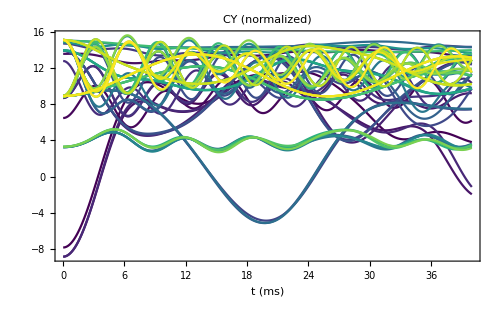

```mathematica
labelPlots={"Norm","C (normalized)", "X (normalized)", "Y (normalized)", "CX (normalized)", "CY (normalized)"};
axesl={"t (ms)",None};
ListPlot[{dt Range[0,Length[#]-1],#}ᵀ&/@(momentsList[[All,All,#]]),Evaluate[optionsListPlot],PlotStyle->colorNodes,PlotLabel->labelPlots[[#]],FrameLabel->axesl]&/@Range[6]
```

#### Field time data

```mathematica
fieldTimeData=Chop[Map[{#[[3]],#[[4]],2(#[[5]]-#[[2]]#[[3]]),2(#[[6]]-#[[2]]#[[4]])}&,momentsList,{2}]];
timeList=dt Range[0,Length[#1]-1]&/@fieldTimeData;
```

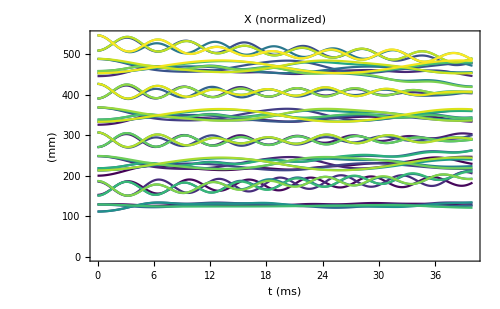
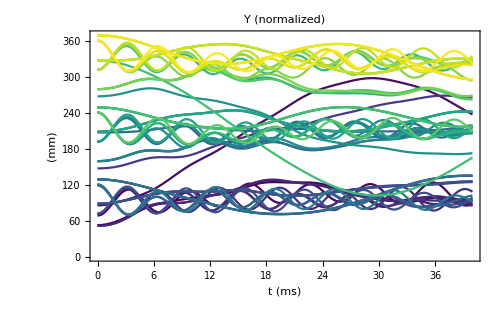
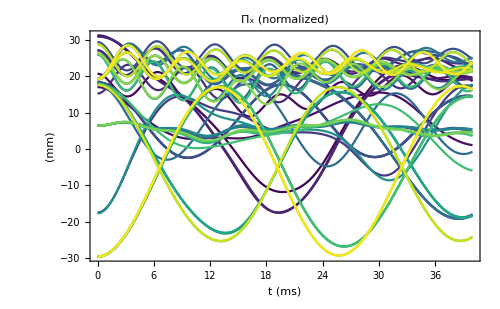
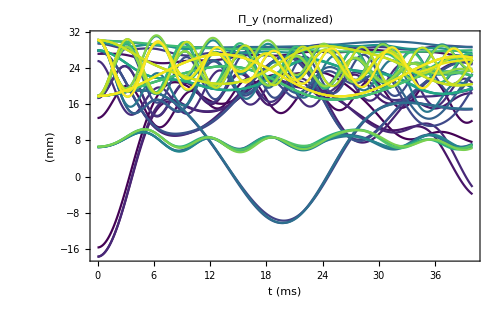

```mathematica
labelPlots={ "X (normalized)", "Y (normalized)", "Π_x (normalized)", "Π_y (normalized)"};
axesl={"t (ms)","(mm)"};
ListPlot[{dt Range[0,Length[#]-1],#}ᵀ&/@(fieldTimeData[[All,All,#]]),Evaluate[optionsListPlot],PlotStyle->colorNodes,PlotLabel->labelPlots[[#]],FrameLabel->axesl]&/@Range[4]
```

#### Mahalanobis distance

```mathematica
weightsInTime=Map[Map[Chop[# #*]&,#]&,solTable];
(*positions=positionsBeads~Join~positionsSprings;*)
weightedDataList=(WeightedData[positions,#]&/@#)&/@weightsInTime;
mahalanobisDistanceList=(With[{cov=Covariance[#],mean=Mean[#]},(√((#-mean).(Inverse[cov].(#-mean)))&/@positions)]&/@#)&/@weightedDataList;
```

```mathematica
distanceThreshold=1.8;
pickConfidenceList=((#<distanceThreshold)&/@#&/@#)&/@mahalanobisDistanceList;
```

#### Molecules

```mathematica
polygons2Dcolorless=Table[MapThread[With[{pts=Pick[positions,#]},If[Length@pts>1,If[CollinearPoints@pts,Nothing,{Opacity[0.05],EdgeForm[],ConvexHullMesh[pts]}],Nothing]]
&,{pickConfidenceList[[i]],timeList[[i]]}],{i,1,Length@pickConfidenceList}];
```

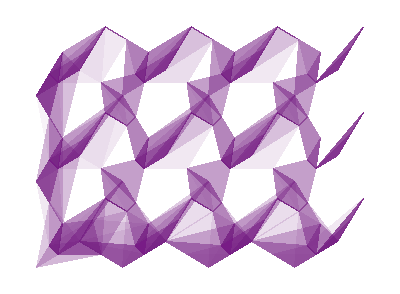

```mathematica
nData=25;
polygonGraphics=Graphics[Map[{RGBColor[0.471412, 0.108766, 0.527016],#1}&,polygons2Dcolorless[[All,;;nData]]]]
```

#### Evolution of centers

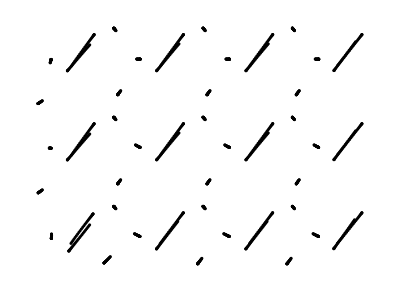

```mathematica
centers=Chop@Flatten[fieldTimeData[[All,;;nData,{1,2}]],1];
Graphics[Disk[#,2]&/@centers]
```

#### Time averages

```mathematica
increasingAverageList[l_List]:=Module[{previous,current},previous=0;Table[current=(previous (i-1)+l[[i]])/i;previous=current;current,{i,1,Length@l}]]
```

```mathematica
iFrame=1;
timeAverageDataList=increasingAverageList[#]&/@(fieldTimeData[[All,iFrame;;,#]])&/@Range[4];
```

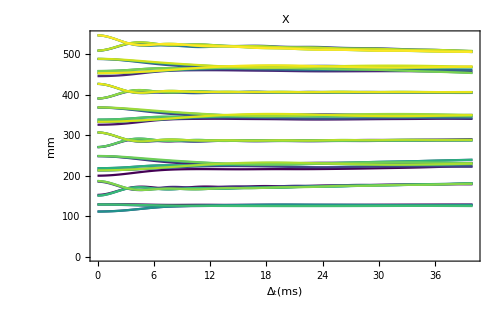
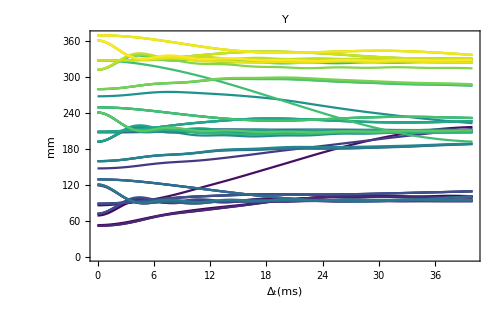
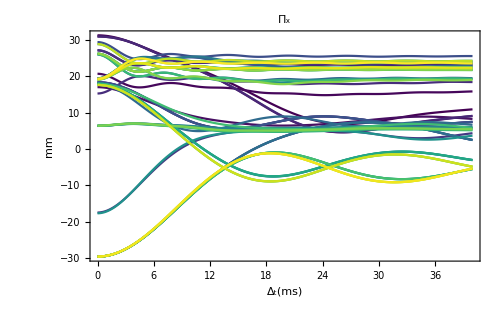
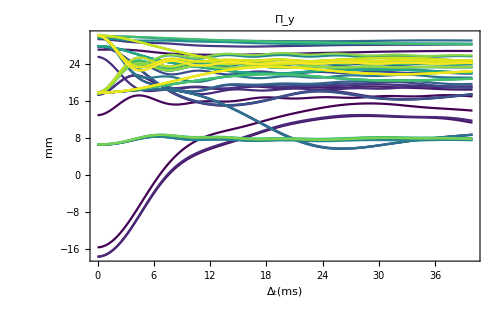

```mathematica
labelPlots={"X","Y","Π_x","Π_y"};
axesl={"Δ_t(ms)","mm"};
ListPlot[{dt Range[0,Length[#]-1],#}ᵀ&/@(timeAverageDataList[[#]]),Evaluate[optionsListPlot],PlotStyle->colorNodes,FrameLabel->axesl,PlotLabel->labelPlots[[#]]]&/@Range[4]
```

```mathematica
30/dt
```

300.

```mathematica
nFramesAverage=nData;
meanAroundDataList=MeanAround[#]&/@(fieldTimeData[[All,iFrame;;iFrame+nFramesAverage-1,#]])&/@Range[4];
meanDataList=Mean[#]&/@(fieldTimeData[[All,iFrame;;iFrame+nFramesAverage-1,#]])&/@Range[4];
stdDataList=StandardDeviation[#]&/@(fieldTimeData[[All,iFrame;;iFrame+nFramesAverage-1,#]])&/@Range[4];
(*Attenstion: this is the angle of the means*)
meanAroundAngleList=ArcTan@@#&/@(meanAroundDataList[[3;;4]]ᵀ);
```

```mathematica
(*angleDataList=Map[ArcTan@@#&,fieldTimeData[[All,iFrame;;iFrame+nFramesAverage-1,{3,4}]],{2}];
(*Attenstion: this is the mean of the angles*)
meanAngleDataList=Mean[#]&/@angleDataList;
stdAngleDataList=StandardDeviation[#]&/@angleDataList;
meanAngleDataList
stdAngleDataList*)
```

```mathematica
refImage=Show[polygonGraphics,Graphics[{Blue,Disk[#,3]&/@(timeAverageDataList[[{1,2},All,nFramesAverage]]ᵀ)}]];
```

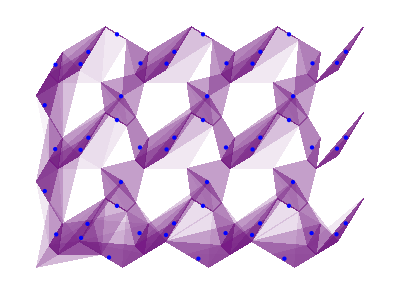

```mathematica
refImage
```

#### Definition of chiral molecules

```mathematica
regionList={};
DynamicModule[{delimiters={}},
Row@{ClickPane[Show[{refImage,Graphics[{Red,Line[Dynamic[delimiters]]}],Graphics[{Blue,Dynamic@regionList}]},ImageSize->Large],AppendTo[delimiters,#1]&],Button["addMolecule",{AppendTo[regionList,Polygon[delimiters]],delimiters={}}]}
]
```

```mathematica
(*Export["moleculesMechanicalHOTI-LinearWannier.mx",regionList];*)
(*Export["moleculesMechanicalHOTI-LinearWannier-polygons.mx",regionList];*)
(*Export["moleculesMechanicalHOTI-LinearWannier-polygons2.mx",regionList]*)
```

```mathematica
regionList=Import["moleculesMechanicalHOTI-LinearWannier-polygons2.mx"];
```

#### Coarse-grained field

```mathematica
rmemberfList=RegionMember[#]&/@regionList;
whichCell[{x_,y_}]:=Module[{i,isMember},
i=1;
isMember=rmemberfList[[i]][{x,y}];
While[isMember==False,isMember=rmemberfList[[i]][{x,y}];i++];
i
]
```

```mathematica
groupByDistanceTimeAverageData=Gather[meanDataListᵀ,whichCell[{#1[[1]],#1[[2]]}]==whichCell[{#2[[1]],#2[[2]]}]&];
coarseGrainedField=({Mean[#[[1]]],Mean[#[[2]]],Total[#[[3]]],Total[#[[4]]]}&@(#ᵀ))&/@groupByDistanceTimeAverageData;
```

```mathematica
groupByDistanceTimeSTDPolData=Gather[(meanDataList[[{1,2}]]~Join~(stdDataList[[{3,4}]]))ᵀ,whichCell[{#1[[1]],#1[[2]]}]==whichCell[{#2[[1]],#2[[2]]}]&];
coarseGrainedSTDPolData=(Sqrt[(#.#)/Length[#]^2]&/@(#[[All,{3,4}]]ᵀ))&/@groupByDistanceTimeSTDPolData;
```

```mathematica
coarseGrainedMeanAngles=ArcTan@@#&/@(coarseGrainedField[[All,{3,4}]]);
```

```mathematica
dfdx[x_,y_]=D[ArcTan[x,y], x];
dfdy[x_,y_]=D[ArcTan[x,y], y];
coarseGrainedSTDAngleData=MapThread[Sqrt[((dfdx@@#1)#2[[1]])^2+((dfdy@@#1)#2[[2]])^2]&,{coarseGrainedField[[All,{3,4}]],coarseGrainedSTDPolData}];
```

#### Graphics

```mathematica
fcolor=GrayLevel[(120-#)/120]&;
barl=BarLegend[{fcolor[#]&,{0,40}},LegendLabel->"Norm",LabelStyle->Directive[Black,FontSize->14]];
primitivesList=MapThread[Module[{center={#1[[1]],#1[[2]]},pol={#1[[3]],#1[[4]]},unitvector,norm,circleRadius=30},
norm=Norm@pol;
unitvector=Normalize[pol];
{fcolor[norm],Thickness[0.01],Arrow[{center-unitvector circleRadius,center+unitvector circleRadius}],Thickness[0.005],Circle[center,circleRadius],Thickness[0.02],Circle[center,circleRadius,{#2-#3,#2+#3}]}
]&,{coarseGrainedField2,coarseGrainedMeanAngles,coarseGrainedSTDAngleData}];
```

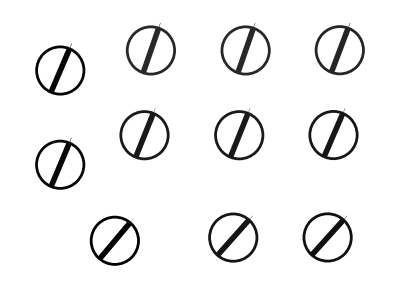

```mathematica
Graphics[primitivesList]
```

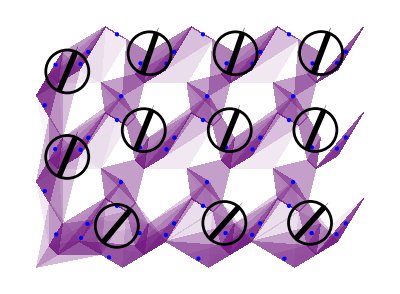

```mathematica
Show[refImage,Graphics[primitivesList]]
```

#### Singularity of the chiral polarization

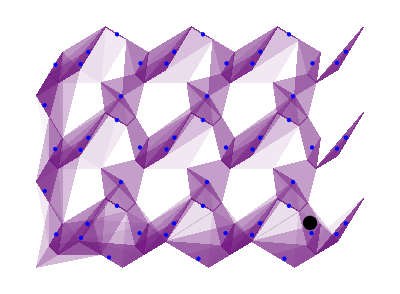

```mathematica
Show[refImage,Graphics[Disk[coarseGrainedField[[3,;;2]],10]]]
```

```mathematica
(coarseGrainedField2[[1,3;;]].{1,0}+coarseGrainedField2[[4,3;;]].{0,1})
```

232.863

### KroneckerDelta initial condition

```mathematica
icKroneckerList=Normal[SparseArray[{#->1},Length[h]]&/@Flatten[Position[pA,1]]];
```

#### Evolution

```mathematica
tf=40;
dt=0.1;
solList=NDSolve[{ⅈ x'[t]==-(h).x[t],x[0]==#},x,{t,0,tf}]&/@icKroneckerList;
solTable=Table[(x[#]/.sol[[1]])&/@Range[0,tf,dt],{sol,solList}];
```

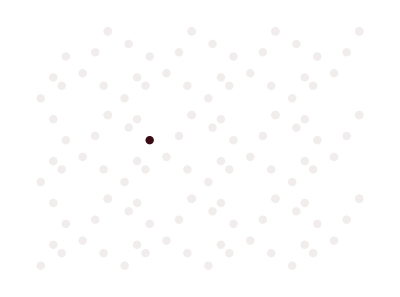

```mathematica
listBlue=ToExpression@;
listRed=ToExpression@;
balanceRedColorMap=Blend[Reverse[RGBColor[#]&/@listRed],#]&;
balanceBlueColorMap=Blend[Reverse[RGBColor[#]&/@listBlue],#]&;
Graphics[{MapThread[{balanceRedColorMap[Abs@#2],Disk[#1,ax/10]}&,{positions,pA solTable[[14,1]]}][[Flatten[Position[pA,1]]]],MapThread[{balanceBlueColorMap[Abs@#2],Disk[#1,ax/10]}&,{positions,pB solTable[[1,1]]}][[Flatten[Position[pB,1]]]]}]
```

#### Moments

```mathematica
momentsList=Quiet@Map[With[{norm2=(#*.#)},
{
Sqrt[norm2],
(#*.(chiral#))/norm2,
1/norm2(#*.(positions[[All,1]]#)),
1/norm2(#*.(positions[[All,2]]#)),
1/norm2(#*.(chiral positions[[All,1]]#)),
1/norm2(#*.(chiral positions[[All,2]]#))
}]&,#]&/@solTable;
```

```mathematica
(*Color map functions*)
githubTextToList[text_String]:=ToExpression[StringReplace[text,{"["->"{","]"->"}"}]];
listViridis=;
viridisCM=Blend[RGBColor[#]&/@listViridis,#]&;
colorNodes=With[{n=Length[icWannierList]},viridisCM[(#-1)/(n-1)]&/@Range[n]];
optionsListPlot={Joined->True,Frame->True,ImageSize->500,PlotRange->All,BaseStyle->{FontSize->25},LabelStyle->Black,FrameStyle->Directive[Black]};
```

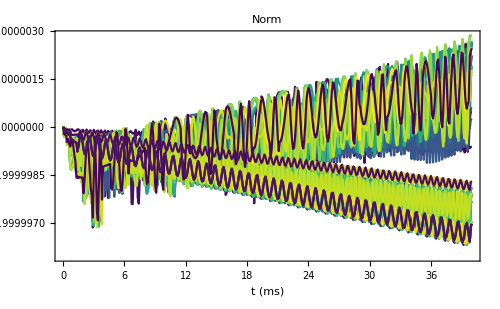
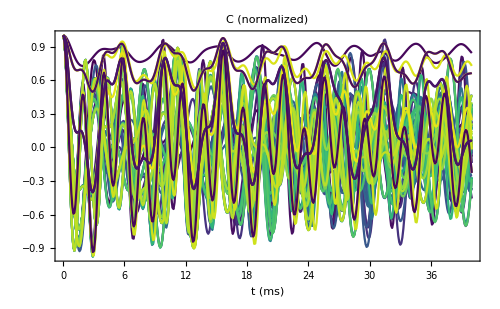
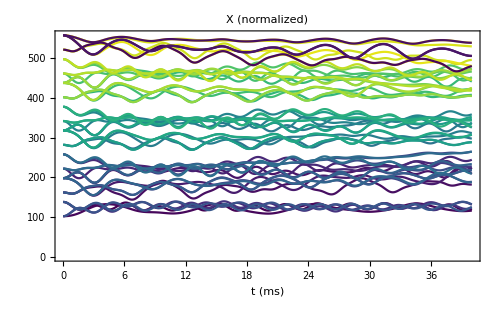
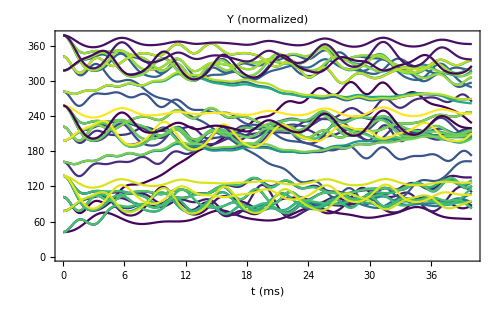
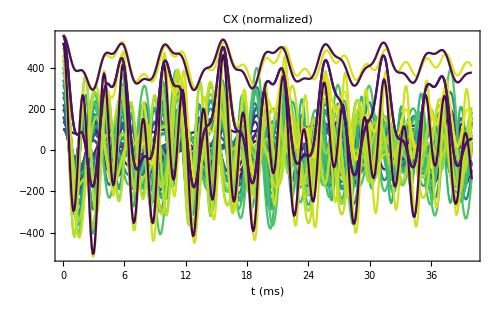
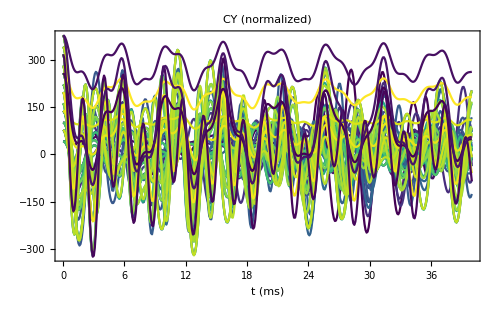

```mathematica
labelPlots={"Norm","C (normalized)", "X (normalized)", "Y (normalized)", "CX (normalized)", "CY (normalized)"};
axesl={"t (ms)",None};
ListPlot[{dt Range[0,Length[#]-1],#}ᵀ&/@(momentsList[[All,All,#]]),Evaluate[optionsListPlot],PlotStyle->colorNodes,PlotLabel->labelPlots[[#]],FrameLabel->axesl]&/@Range[6]
```

#### Field time data

```mathematica
fieldTimeData=Chop[Map[{#[[3]],#[[4]],2(#[[5]]-#[[2]]#[[3]]),2(#[[6]]-#[[2]]#[[4]])}&,momentsList,{2}]];
(*we skip the first frame since it is singular in the covariance matrix*)
fieldTimeData=fieldTimeData[[All,2;;]];
timeList=dt Range[0,Length[#1]-1]&/@fieldTimeData;
```

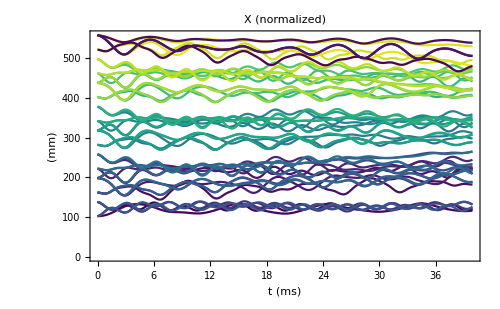
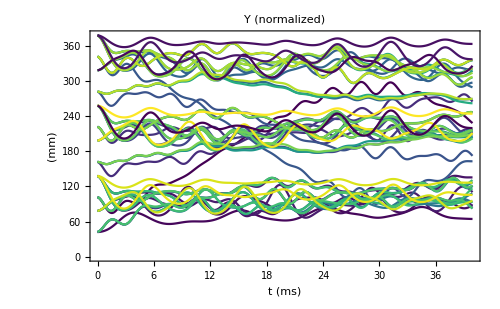
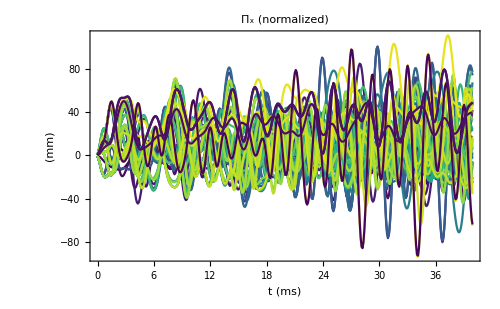
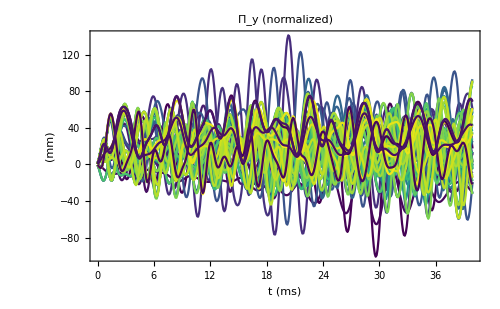

```mathematica
labelPlots={ "X (normalized)", "Y (normalized)", "Π_x (normalized)", "Π_y (normalized)"};
axesl={"t (ms)","(mm)"};
ListPlot[{dt Range[0,Length[#]-1],#}ᵀ&/@(fieldTimeData[[All,All,#]]),Evaluate[optionsListPlot],PlotStyle->colorNodes,PlotLabel->labelPlots[[#]],FrameLabel->axesl]&/@Range[4]
```

#### Mahalanobis distance

```mathematica
weightsInTime=Map[Map[Chop[# #*]&,#]&,solTable[[All,2;;]]];(*skip the first frame due to sinuglarity in covariance*)
(*positions=positionsBeads~Join~positionsSprings;*)
weightedDataList=(WeightedData[positions,#]&/@#)&/@weightsInTime;
mahalanobisDistanceList=(With[{cov=Covariance[#],mean=Mean[#]},(√((#-mean).(Inverse[cov].(#-mean)))&/@positions)]&/@#)&/@weightedDataList;
```

```mathematica
distanceThreshold=1.5;
pickConfidenceList=((#<distanceThreshold)&/@#&/@#)&/@mahalanobisDistanceList;
```

#### Molecules

```mathematica
polygons2Dcolorless=Table[MapThread[With[{pts=Pick[positions,#]},If[Length@pts>1,If[CollinearPoints@pts,Nothing,{Opacity[0.05],EdgeForm[],ConvexHullMesh[pts]}],Nothing]]
&,{pickConfidenceList[[i]],timeList[[i]]}],{i,1,Length@pickConfidenceList}];
```

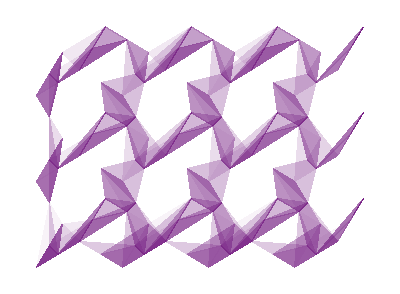

```mathematica
nData=20;
polygonGraphics=Graphics[Map[{RGBColor[0.471412, 0.108766, 0.527016],#1}&,polygons2Dcolorless[[All,;;nData]]]]
```

#### Evolution of centers

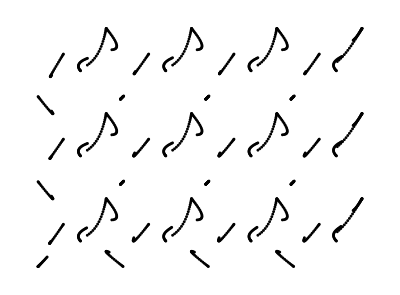

```mathematica
centers=Chop@Flatten[fieldTimeData[[All,;;nData,{1,2}]],1];
Graphics[Disk[#,2]&/@centers]
```

#### Time averages

```mathematica
increasingAverageList[l_List]:=Module[{previous,current},previous=0;Table[current=(previous (i-1)+l[[i]])/i;previous=current;current,{i,1,Length@l}]]
```

```mathematica
iFrame=1;
timeAverageDataList=increasingAverageList[#]&/@(fieldTimeData[[All,iFrame;;,#]])&/@Range[4];
```

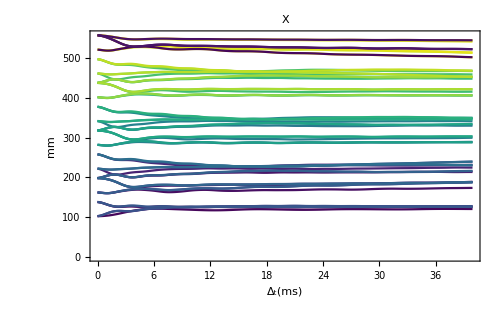
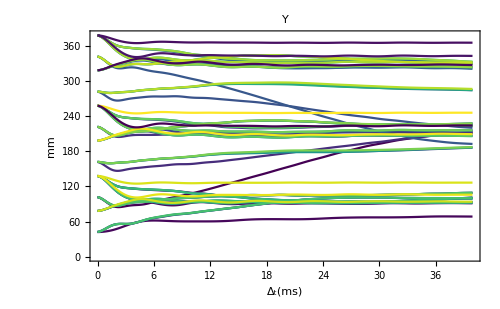
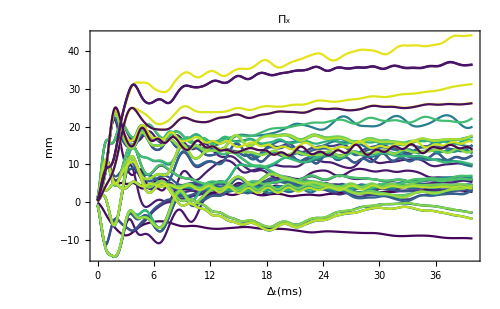
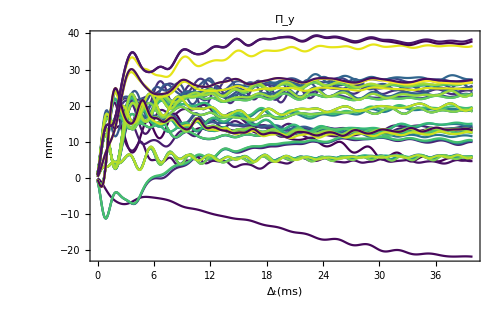

```mathematica
labelPlots={"X","Y","Π_x","Π_y"};
axesl={"Δ_t(ms)","mm"};
ListPlot[{dt Range[0,Length[#]-1],#}ᵀ&/@(timeAverageDataList[[#]]),Evaluate[optionsListPlot],PlotStyle->colorNodes,FrameLabel->axesl,PlotLabel->labelPlots[[#]]]&/@Range[4]
```

```mathematica
30/dt
```

300.

```mathematica
nFramesAverage=nData;
meanAroundDataList=MeanAround[#]&/@(fieldTimeData[[All,iFrame;;iFrame+nFramesAverage-1,#]])&/@Range[4];
meanDataList=Mean[#]&/@(fieldTimeData[[All,iFrame;;iFrame+nFramesAverage-1,#]])&/@Range[4];
stdDataList=StandardDeviation[#]&/@(fieldTimeData[[All,iFrame;;iFrame+nFramesAverage-1,#]])&/@Range[4];
(*Attenstion: this is the angle of the means*)
meanAroundAngleList=ArcTan@@#&/@(meanAroundDataList[[3;;4]]ᵀ);
```

```mathematica
(*angleDataList=Map[ArcTan@@#&,fieldTimeData[[All,iFrame;;iFrame+nFramesAverage-1,{3,4}]],{2}];
(*Attenstion: this is the mean of the angles*)
meanAngleDataList=Mean[#]&/@angleDataList;
stdAngleDataList=StandardDeviation[#]&/@angleDataList;
meanAngleDataList
stdAngleDataList*)
```

```mathematica
refImage=Show[polygonGraphics,Graphics[{Blue,Disk[#,3]&/@(timeAverageDataList[[{1,2},All,nFramesAverage]]ᵀ)}]];
```

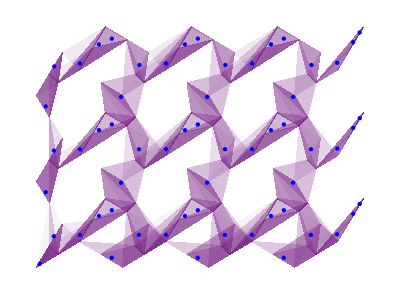

```mathematica
refImage
```

#### Definition of chiral molecules

```mathematica
regionList={};
DynamicModule[{delimiters={}},
Row@{ClickPane[Show[{refImage,Graphics[{Red,Line[Dynamic[delimiters]]}],Graphics[{Blue,Dynamic@regionList}]},ImageSize->Large],AppendTo[delimiters,#1]&],Button["addMolecule",{AppendTo[regionList,Polygon[delimiters]],delimiters={}}]}
]
```

```mathematica
(*Export["moleculesMechanicalHOTI-LinearDelta.mx",regionList];*)
(*Export["moleculesMechanicalHOTI-LinearDelta-polygons.mx",regionList];*)
```

```mathematica
regionList=Import["moleculesMechanicalHOTI-LinearDelta-polygons.mx"];
```

#### Coarse-grained field

```mathematica
rmemberfList=RegionMember[#]&/@regionList;
whichCell[{x_,y_}]:=Module[{i,isMember},
i=1;
isMember=rmemberfList[[i]][{x,y}];
While[isMember==False,isMember=rmemberfList[[i]][{x,y}];i++];
i
]
```

```mathematica
groupByDistanceTimeAverageData=Gather[meanDataListᵀ,whichCell[{#1[[1]],#1[[2]]}]==whichCell[{#2[[1]],#2[[2]]}]&];
coarseGrainedField=({Mean[#[[1]]],Mean[#[[2]]],Total[#[[3]]],Total[#[[4]]]}&@(#ᵀ))&/@groupByDistanceTimeAverageData;
```

```mathematica
groupByDistanceTimeSTDPolData=Gather[(meanDataList[[{1,2}]]~Join~(stdDataList[[{3,4}]]))ᵀ,whichCell[{#1[[1]],#1[[2]]}]==whichCell[{#2[[1]],#2[[2]]}]&];
coarseGrainedSTDPolData=(Sqrt[(#.#)/Length[#]^2]&/@(#[[All,{3,4}]]ᵀ))&/@groupByDistanceTimeSTDPolData;
```

```mathematica
coarseGrainedMeanAngles=ArcTan@@#&/@(coarseGrainedField[[All,{3,4}]]);
```

```mathematica
dfdx[x_,y_]=D[ArcTan[x,y], x];
dfdy[x_,y_]=D[ArcTan[x,y], y];
coarseGrainedSTDAngleData=MapThread[Sqrt[((dfdx@@#1)#2[[1]])^2+((dfdy@@#1)#2[[2]])^2]&,{coarseGrainedField[[All,{3,4}]],coarseGrainedSTDPolData}];
```

#### Graphics

```mathematica
fcolor=GrayLevel[(120-#)/120]&;
barl=BarLegend[{fcolor[#]&,{0,40}},LegendLabel->"Norm",LabelStyle->Directive[Black,FontSize->14]];
primitivesList=MapThread[Module[{center={#1[[1]],#1[[2]]},pol={#1[[3]],#1[[4]]},unitvector,norm,circleRadius=30},
norm=Norm@pol;
unitvector=Normalize[pol];
{fcolor[norm],Thickness[0.01],Arrow[{center-unitvector circleRadius,center+unitvector circleRadius}],Thickness[0.005],Circle[center,circleRadius],Thickness[0.02],Circle[center,circleRadius,{#2-#3,#2+#3}]}
]&,{coarseGrainedField,coarseGrainedMeanAngles,coarseGrainedSTDAngleData}];
```

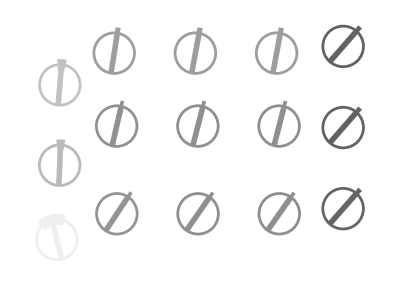

```mathematica
Graphics[primitivesList]
```

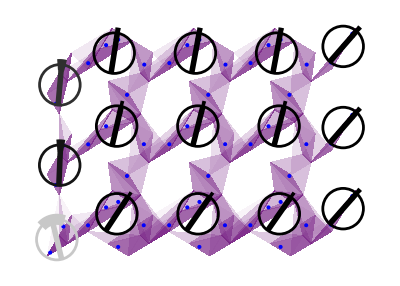

```mathematica
Show[refImage,Graphics[primitivesList]]
```

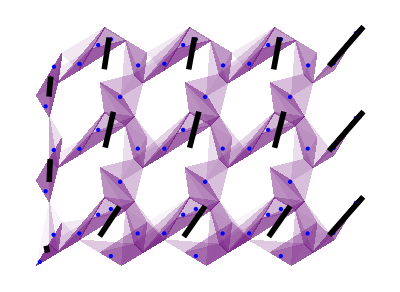

```mathematica
primitivesList2=MapThread[Module[{center={#1[[1]],#1[[2]]},pol={#1[[3]],#1[[4]]},unitvector,norm,circleRadius=30},
norm=Norm@pol;
unitvector=Normalize[pol];
{Black,Thickness[0.01],Arrow[{center-pol/2,center+pol/2}]}
]&,{coarseGrainedField,coarseGrainedMeanAngles,coarseGrainedSTDAngleData}];
Show[refImage,Graphics[primitivesList2]]
```

#### Singularity of the chiral polarization

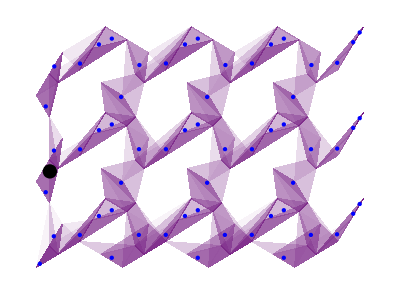

```mathematica
Show[refImage,Graphics[Disk[coarseGrainedField[[3,;;2]],10]]]
```

```mathematica
((coarseGrainedField[[2,3;;]]-coarseGrainedField[[1,3;;]]).{1,0}+(coarseGrainedField[[3,3;;]]-coarseGrainedField[[1,3;;]]).{0,1})
```

54.4428

### Gaussian initial condition

```mathematica
fGaussian[pos_,center_,σ_:ax/3]:=ⅇ^((-(center-pos).(center-pos))/(2 σ^2));
```

```mathematica
icGaussianList=Table[Quiet@Normalize[fGaussian[#,positions[[i]]]&/@positions],{i,Flatten[Position[pA,1]]}];
```

#### Evolution

```mathematica
tf=40;
dt=0.1;
solList=NDSolve[{ⅈ x'[t]==-(h).x[t],x[0]==#},x,{t,0,tf}]&/@icGaussianList;
solTable=Table[(x[#]/.sol[[1]])&/@Range[0,tf,dt],{sol,solList}];
```

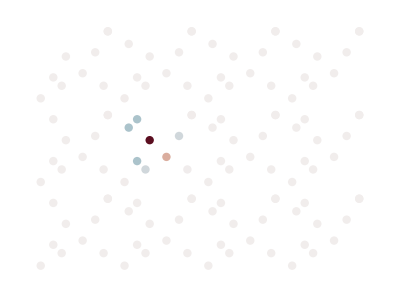

```mathematica
listBlue=ToExpression@;
listRed=ToExpression@;
balanceRedColorMap=Blend[Reverse[RGBColor[#]&/@listRed],#]&;
balanceBlueColorMap=Blend[Reverse[RGBColor[#]&/@listBlue],#]&;
Graphics[{MapThread[{balanceRedColorMap[Abs@#2],Disk[#1,ax/10]}&,{positions,pA solTable[[14,1]]}][[Flatten[Position[pA,1]]]],MapThread[{balanceBlueColorMap[Abs@#2],Disk[#1,ax/10]}&,{positions,pB solTable[[14,1]]}][[Flatten[Position[pB,1]]]]}]
```

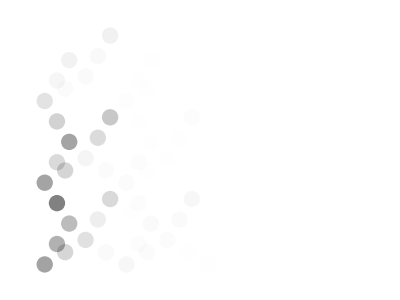

```mathematica
Graphics[MapThread[{Opacity[Abs[#2]],Disk[#1,ax/5]}&,{positions,solTable[[1,100]]}]]
```

#### Moments

```mathematica
momentsList=Quiet@Map[With[{norm2=(#*.#)},
{
Sqrt[norm2],
(#*.(chiral#))/norm2,
1/norm2(#*.(positions[[All,1]]#)),
1/norm2(#*.(positions[[All,2]]#)),
1/norm2(#*.(chiral positions[[All,1]]#)),
1/norm2(#*.(chiral positions[[All,2]]#))
}]&,#]&/@solTable;
```

```mathematica
(*Color map functions*)
githubTextToList[text_String]:=ToExpression[StringReplace[text,{"["->"{","]"->"}"}]];
listViridis=;
viridisCM=Blend[RGBColor[#]&/@listViridis,#]&;
colorNodes=With[{n=Length[icWannierList]},viridisCM[(#-1)/(n-1)]&/@Range[n]];
optionsListPlot={Joined->True,Frame->True,ImageSize->500,PlotRange->All,BaseStyle->{FontSize->25},LabelStyle->Black,FrameStyle->Directive[Black]};
```

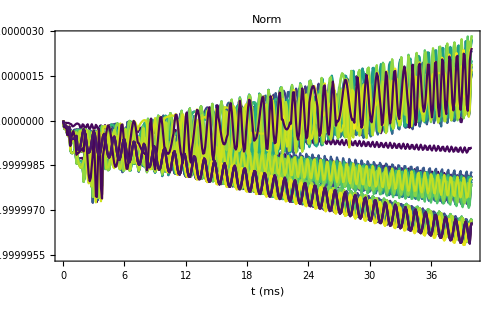
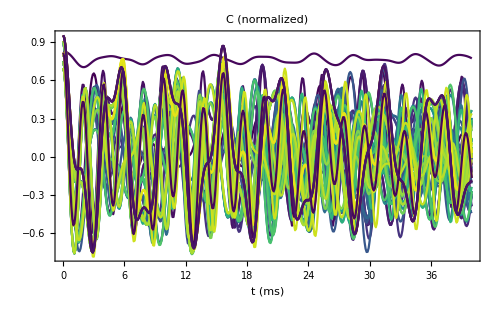
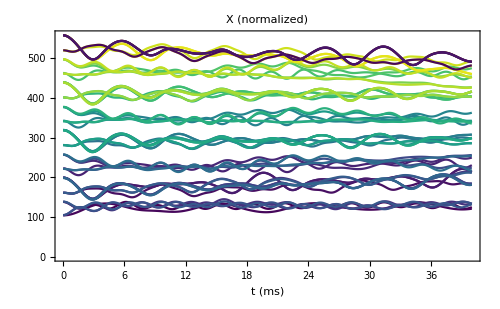
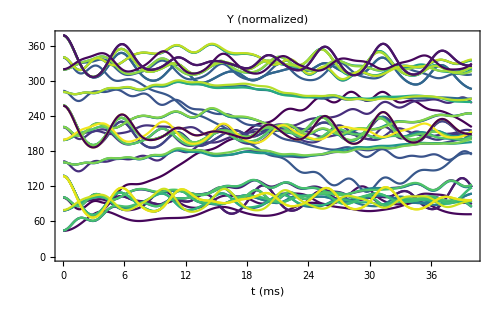
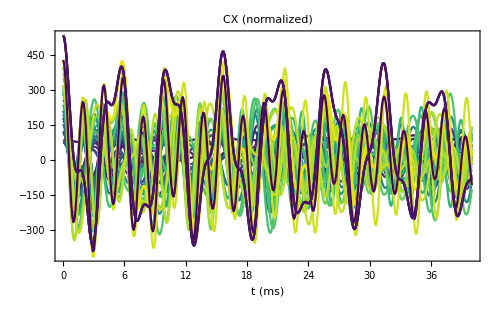
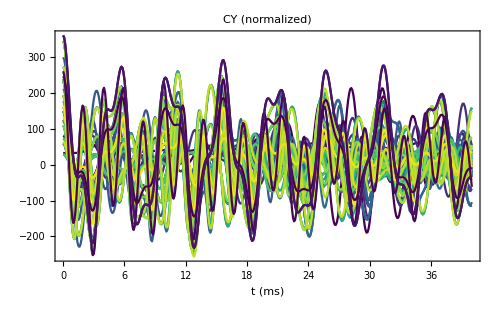

```mathematica
labelPlots={"Norm","C (normalized)", "X (normalized)", "Y (normalized)", "CX (normalized)", "CY (normalized)"};
axesl={"t (ms)",None};
ListPlot[{dt Range[0,Length[#]-1],#}ᵀ&/@(momentsList[[All,All,#]]),Evaluate[optionsListPlot],PlotStyle->colorNodes,PlotLabel->labelPlots[[#]],FrameLabel->axesl]&/@Range[6]
```

#### Field time data

```mathematica
fieldTimeData=Chop[Map[{#[[3]],#[[4]],2(#[[5]]-#[[2]]#[[3]]),2(#[[6]]-#[[2]]#[[4]])}&,momentsList,{2}]];
timeList=dt Range[0,Length[#1]-1]&/@fieldTimeData;
```

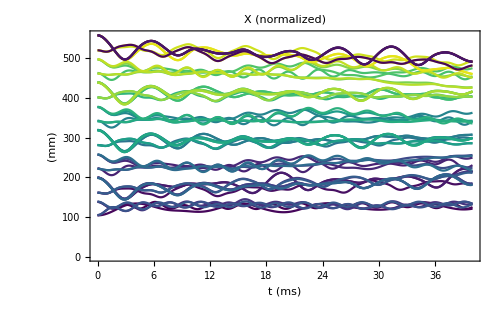
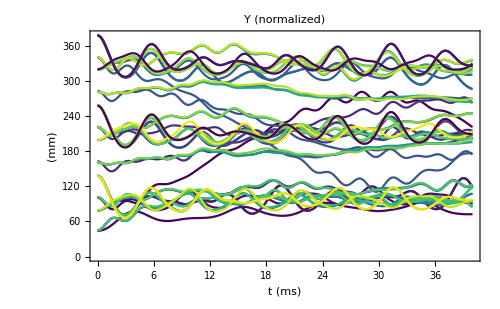
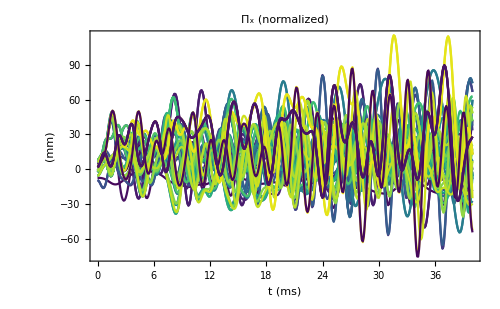
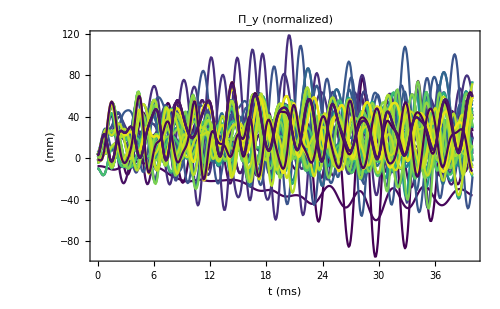

```mathematica
labelPlots={ "X (normalized)", "Y (normalized)", "Π_x (normalized)", "Π_y (normalized)"};
axesl={"t (ms)","(mm)"};
ListPlot[{dt Range[0,Length[#]-1],#}ᵀ&/@(fieldTimeData[[All,All,#]]),Evaluate[optionsListPlot],PlotStyle->colorNodes,PlotLabel->labelPlots[[#]],FrameLabel->axesl]&/@Range[4]
```

#### Mahalanobis distance

```mathematica
weightsInTime=Map[Map[Chop[# #*]&,#]&,solTable];
(*positions=positionsBeads~Join~positionsSprings;*)
weightedDataList=(WeightedData[positions,#]&/@#)&/@weightsInTime;
mahalanobisDistanceList=(With[{cov=Covariance[#],mean=Mean[#]},(√((#-mean).(Inverse[cov].(#-mean)))&/@positions)]&/@#)&/@weightedDataList;
```

```mathematica
distanceThreshold=1.;
pickConfidenceList=((#<distanceThreshold)&/@#&/@#)&/@mahalanobisDistanceList;
```

#### Molecules

```mathematica
polygons2Dcolorless=Table[MapThread[With[{pts=Pick[positions,#]},If[Length@pts>1,If[CollinearPoints@pts,Nothing,{Opacity[0.05],EdgeForm[],ConvexHullMesh[pts]}],Nothing]]
&,{pickConfidenceList[[i]],timeList[[i]]}],{i,1,Length@pickConfidenceList}];
```

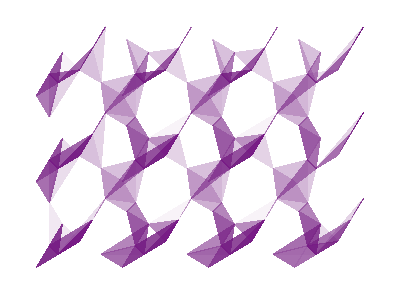

```mathematica
nData=25;
polygonGraphics=Graphics[Map[{RGBColor[0.471412, 0.108766, 0.527016],#1}&,polygons2Dcolorless[[All,;;nData]]]]
```

#### Evolution of centers

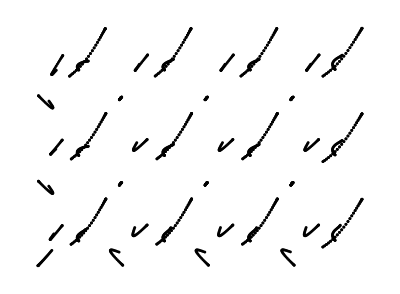

```mathematica
centers=Chop@Flatten[fieldTimeData[[All,;;nData,{1,2}]],1];
Graphics[Disk[#,2]&/@centers]
```

#### Time averages

```mathematica
increasingAverageList[l_List]:=Module[{previous,current},previous=0;Table[current=(previous (i-1)+l[[i]])/i;previous=current;current,{i,1,Length@l}]]
```

```mathematica
iFrame=1;
timeAverageDataList=increasingAverageList[#]&/@(fieldTimeData[[All,iFrame;;,#]])&/@Range[4];
```

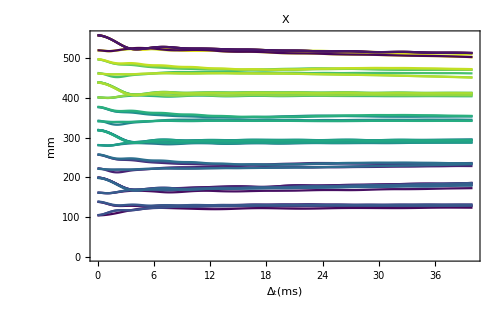
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
labelPlots={"X","Y","Π_x","Π_y"};
axesl={"Δ_t(ms)","mm"};
ListPlot[{dt Range[0,Length[#]-1],#}ᵀ&/@(timeAverageDataList[[#]]),Evaluate[optionsListPlot],PlotStyle->colorNodes,FrameLabel->axesl,PlotLabel->labelPlots[[#]]]&/@Range[4]
```

```mathematica
30/dt
```

300.

```mathematica
nFramesAverage=nData;
meanAroundDataList=MeanAround[#]&/@(fieldTimeData[[All,iFrame;;iFrame+nFramesAverage-1,#]])&/@Range[4];
meanDataList=Mean[#]&/@(fieldTimeData[[All,iFrame;;iFrame+nFramesAverage-1,#]])&/@Range[4];
stdDataList=StandardDeviation[#]&/@(fieldTimeData[[All,iFrame;;iFrame+nFramesAverage-1,#]])&/@Range[4];
(*Attenstion: this is the angle of the means*)
meanAroundAngleList=ArcTan@@#&/@(meanAroundDataList[[3;;4]]ᵀ);
```

```mathematica
(*angleDataList=Map[ArcTan@@#&,fieldTimeData[[All,iFrame;;iFrame+nFramesAverage-1,{3,4}]],{2}];
(*Attenstion: this is the mean of the angles*)
meanAngleDataList=Mean[#]&/@angleDataList;
stdAngleDataList=StandardDeviation[#]&/@angleDataList;
meanAngleDataList
stdAngleDataList*)
```

```mathematica
refImage=Show[polygonGraphics,Graphics[{Blue,Disk[#,3]&/@(timeAverageDataList[[{1,2},All,nFramesAverage]]ᵀ)}]];
```

```mathematica
refImage
```

-Graphics-

#### Definition of chiral molecules

```mathematica
regionList={};
DynamicModule[{delimiters={}},
Row@{ClickPane[Show[{refImage,Graphics[{Red,Line[Dynamic[delimiters]]}],Graphics[{Blue,Dynamic@regionList}]},ImageSize->Large],AppendTo[delimiters,#1]&],Button["addMolecule",{AppendTo[regionList,Polygon[delimiters]],delimiters={}}]}
]
```

```mathematica
(*Export["moleculesMechanicalHOTI-LinearGaussian-polygons.mx",regionList];*)
```

```mathematica
regionList=Import["moleculesMechanicalHOTI-LinearGaussian-polygons.mx"];
```

#### Coarse-grained field

```mathematica
rmemberfList=RegionMember[#]&/@regionList;
whichCell[{x_,y_}]:=Module[{i,isMember},
i=1;
isMember=rmemberfList[[i]][{x,y}];
While[isMember==False,isMember=rmemberfList[[i]][{x,y}];i++];
i
]
```

```mathematica
groupByDistanceTimeAverageData=Gather[meanDataListᵀ,whichCell[{#1[[1]],#1[[2]]}]==whichCell[{#2[[1]],#2[[2]]}]&];
coarseGrainedField=({Mean[#[[1]]],Mean[#[[2]]],Total[#[[3]]],Total[#[[4]]]}&@(#ᵀ))&/@groupByDistanceTimeAverageData;
```

```mathematica
groupByDistanceTimeSTDPolData=Gather[(meanDataList[[{1,2}]]~Join~(stdDataList[[{3,4}]]))ᵀ,whichCell[{#1[[1]],#1[[2]]}]==whichCell[{#2[[1]],#2[[2]]}]&];
coarseGrainedSTDPolData=(Sqrt[(#.#)/Length[#]^2]&/@(#[[All,{3,4}]]ᵀ))&/@groupByDistanceTimeSTDPolData;
```

```mathematica
coarseGrainedMeanAngles=ArcTan@@#&/@(coarseGrainedField[[All,{3,4}]]);
```

```mathematica
dfdx[x_,y_]=D[ArcTan[x,y], x];
dfdy[x_,y_]=D[ArcTan[x,y], y];
coarseGrainedSTDAngleData=MapThread[Sqrt[((dfdx@@#1)#2[[1]])^2+((dfdy@@#1)#2[[2]])^2]&,{coarseGrainedField[[All,{3,4}]],coarseGrainedSTDPolData}];
```

#### Graphics

```mathematica
fcolor=GrayLevel[(120-#)/120]&;
barl=BarLegend[{fcolor[#]&,{0,40}},LegendLabel->"Norm",LabelStyle->Directive[Black,FontSize->14]];
primitivesList=MapThread[Module[{center={#1[[1]],#1[[2]]},pol={#1[[3]],#1[[4]]},unitvector,norm,circleRadius=30},
norm=Norm@pol;
unitvector=Normalize[pol];
{fcolor[norm],Thickness[0.01],Arrow[{center-unitvector circleRadius,center+unitvector circleRadius}],Thickness[0.005],Circle[center,circleRadius],Thickness[0.02],Circle[center,circleRadius,{#2-#3,#2+#3}]}
]&,{coarseGrainedField,coarseGrainedMeanAngles,coarseGrainedSTDAngleData}];
```

```mathematica
Graphics[primitivesList]
```

-Graphics-

```mathematica
Show[refImage,Graphics[primitivesList]]
```

-Graphics-

```mathematica
primitivesList2=MapThread[Module[{center={#1[[1]],#1[[2]]},pol={#1[[3]],#1[[4]]},unitvector,norm,circleRadius=30},
norm=Norm@pol;
unitvector=Normalize[pol];
{Black,Thickness[0.01],Arrow[{center-pol/2,center+pol/2}]}
]&,{coarseGrainedField,coarseGrainedMeanAngles,coarseGrainedSTDAngleData}];
```

```mathematica
Show[refImage,Graphics[primitivesList2]]
```

-Graphics-

#### Singularity of the chiral polarization

```mathematica
Show[refImage,Graphics[Disk[coarseGrainedField[[2,;;2]],10]]]
```

-Graphics-

```mathematica
((coarseGrainedField[[2,3;;]]-coarseGrainedField[[1,3;;]]).{1,0}+(coarseGrainedField[[3,3;;]]-coarseGrainedField[[1,3;;]]).{0,1})
```

93.2498